```mathematica
Ex vivo Magnetic Resonance Diffusion Weighted Imaging in Congenital Heart Disease,an Insight into the Microstructures of Tetralogy of Fallot, Biventricular and Univentricular Systemic Right Ventricle

Please, acknowledge the work by citing the article entitled 
Ex vivo Magnetic Resonance Diffusion Weighted Imaging in Congenital Heart Disease,an Insight into the Microstructures of Tetralogy of Fallot,Biventricular and Univentricular Systemic Right Ventricle (Tous et al, 2020)
from the Journal of Cardiovascular Magnetic Resonance Imaging. This sequence was part of a comparison between SE monopolar,SE bipolar, STEAM monopolar, TRSE and TRSE adjusted to scan long term (~40 years)formalin fixed specimens with low T2 (~20ms). The scans were performed on a 3T Skyra bought in the early 2010(43mT/m gradient amplitude, 180 mT/m/ms slew rate).

TRSE and TRSE adjusted:
```

```mathematica
Author Names:Cyril Tous 1,2,Thomas L.Gentles 3,Alistair A.Young 1,4,Beau Pontré 1
Author Affiliations:
1Department of Anatomy and Medical Imaging,University of Auckland,Auckland,New Zealand
2Laboratory of Clinical Image Processing Le Centre de Recherche du Centre Hospitalier de l’Université de Montréal,Canada
3Green Lane Paediatric and Congenital Cardiac Service,Starship Children’s Hospital,Auckland,New Zealand
4Department of Biomedical Engineering,King’s College London,UK

Corresponding Author Info:
Beau Pontré,
Department of Anatomy and Radiology,
University of Auckland,
b.pontre@auckland.ac.nz

Cyril Tous
cyriltous@gmail.com

(* modified mathematica from (Mattiello et al, 1995) and  (Zubkov et al, 2014) *)
Date         :   22/09/2017;
Input        :    Known sequence diagram of the diffusion sequence  with the timing and  gradients' amplitude;
Output   :     B matrix [ndir, 6]  with ndir the number of diffusion directions, and Bmatrix[1,:]= [Bxx, Byy, Bzz, 2Bxy, 2Bxz, 2Byz];
Goal         :
=>Generating the B matrix from the known sequence diagram; 
    =>determining M0=F=Integral(g(t)), M1=Integral(t*g(t)), M2=Integral(t^2*g(t)) for the zeroth moment, first moment, second moment;
    => Calculating velocity shift Kv=γ*M1,d=Integral(F^2), Maxwell gradient moment =Integral(g(t)^2);

method  :      References:
-'Spin Diffusion Measurements:Spin Echoes in the Presence of a Time-Dependent Field Gradient' (STEjskal and Tanner, 1965);
-'Tissue Perfusion in Humans Studied by Fourier Velocity Distribution, Line Scan, and Echo Planar Imaging'(Feinberg, 1990);
- 'Analytical expressions for the b matrix in NMR diffusion Imaging and Spectroscopy' (Mattiello et al, 1993);
- 'Estimation of the Effective Self Diffusion TEnsor from the NMR Spin Echo' (Basser et al, 1993);
- 'Part II Analytical Calculation of the b Matrix in Diffusion Imaging'(Mattiello et al, 1995); => (Mathematica);
- 'Pusled-Field Gradient Nuclear Magnetic Resonance as a tool for studying translational diffusion:Part 1Basic Theory' (Price 1997);
- 'The b matrix in diffusion TEnsor echo planar imaging' (Mattiello et al, 1997);
-'Reduction of eddy-current-induced distortion in diffusion MRI using a twice-refocused spin echo'(Reese,2003);
-'Handbook of MRI Pulse Sequences (Bernstein, King, Zhou, 2004)'
-'Double spin echo diffusion weighting with a modified eddy current adjustment'(Finsterbusch, 2010);
- 'Efficient and precise calculation of the b matrix elements in diffusion weigthed imaging pulse sequences' (Zubkov et al, 2014);
=> (Mathematica);
-'Orthogonalizing crusher and diffusion-encoding gradients to suppress undesired echo pathways in the twice-refocused spin echo diffusion sequence'(Nagy, 2014);
```

```mathematica
"Double-spin-echo diffusion weighting with a modified eddy current adjustment (Finsterbusch,2010)";
 "code adapted from: Pusled-Field Gradient Nuclear Magnetic Resonance as a tool for studying translational diffusion:Part 1Basic Theory (Price 1997), (Maple)";
ClearAll["Global`*"]
F[g_,ti_]=∫_ti^t gⅆtd;
g1=0;
l1=0;
F1=F[g1,l1];

l2=t1;
g2=g;
F2=Replace[F1,t->l2,All] + F[g2,l2];

l3=t1+δ1;
g3=0;
F3=Replace[F2,t->l3,All] +  F[g3,l3];

l4=t1+δ1+d;
g4=g; 
F4=Replace[F3,t->l4,All] +  F[g4,l4] ;

l5=t1+δ1+d+ δ2 ;
g5=0;
F5=Replace[F4,t->l5,All]+F[g5,l5];

l6=t1+Δ;
g6=-g;  
F6=Replace[F5,t->l6,All]+F[g6,l6];

l7=t1+Δ+δ11;
g7=0;
F7=Replace[F6,t->l7,All]+F[g7,l7];

l8=t1+Δ+δ11+d;
g8=-g; 
F8=Replace[F7,t->l8,All]+F[g8,l8];

l9=t1+Δ+δ11+d+δ22;
g9=0;
F9=Replace[F8,t->l9,All]+F[g9,l9];

l10=TE;

T1=l3+d/2;
T2=l7+d/2;

(* Define the function "f" [=F(tau)] = Integration between the two RF180 *)
f1=F3;
f2=F7;

γ=2.*Pi*42.5756*1000000.;
g=42.*10^-6;
δ1=6020.*10^-6;
δ2=14040.*10^-6;
δ11=10970.*10^-6;
δ22=9090.*10^-6;
TE=62500.*10^-6;
d=5440.*10^-6;
t1=3420.*10^-6;
ϵ=400.*10^-6;
δ=δ1+δ2;
Δ=δ+d+2ϵ;

(* Define the integral of F between the two RF180 with time at 1st RF180 is T1 and time at 2nd RF180 is T2 *)
FT1toT2=Simplify[Integrate[F3,{t,T1,l4}]+Integrate[F4,{t,l4,l5}]+Integrate[F5,{t,l5,l6}]+Integrate[F6,{t,l6,l7}]+Integrate[F7,{t,l7,T2}]];
FT2toTE= Simplify[Integrate[F7,{t,T2,l8}]+Integrate[F8,{t,l8,l9}]+Integrate[F9,{t,l9,TE}]];
FT1toTE=FT1toT2+FT2toTE;

FINT= Simplify[Integrate[F1,{t,l1,l2}]+Integrate[F2,{t,l2,l3}]+ Integrate[F3,{t,l3,l4}]+Integrate[F4,{t,l4,l5}]+Integrate[F,{t,l5,l6}]+Integrate[F6,{t,l6,l7}]+Integrate[F7,{t,l7,l8}]+Integrate[F8,{t,l8,l9}]+Integrate[F9,{t,l9,l10}]];

(* Define the integral of F^2 between 0 and 2τ *)
FSQINT = Simplify[Integrate[F1^2,{t,l1,l2}]+Integrate[F2^2,{t,l2,l3}]+ Integrate[F3^2,{t,l3,l4}]+Integrate[F4^2,{t,l4,l5}]+Integrate[F5^2,{t,l5,l6}]+Integrate[F6^2,{t,l6,l7}]+Integrate[F7^2,{t,l7,l8}]+Integrate[F8^2,{t,l8,l9}]+Integrate[F9^2,{t,l9,l10}]];
```

```mathematica
(* with b= Integral[F^2,{t,0,TE}]*)
bfound=Simplify[γ^2*FSQINT/.{(TE-t1)->(δ1+d+δ2+δ11+d+δ22),δ->δ1+δ2,Δ->δ1+δ2+d,δ11->δ1+δ2-δ22}];
(*1/3 g^2 γ^2 (2 (δ1+δ2)^3+3 d (δ1^2+δ22^2))*) (* 801.59*)

(* Stejskal and Tanner*)
bfound=Simplify[γ^2*FSQINT/.{(TE-t1)->(δ1+d+δ2+δ11+d+δ22),δ11->δ1+δ2-δ22,d->0}]/.δ1+δ2->δ/.-δ1-δ2->-δ;
(* 1/3 g^2 γ^2 δ^2 (-δ+3 Δ) *) (* 801.59*)

bFinsterbusch=Simplify[(γ^2*g^2*(δ^2*(Δ-δ/3)-2δ*δ2*d+d*(δ2^2+δ22^2)))/.δ->δ1+δ2/.Δ->δ1+δ2+d];
(*1/3 g^2 γ^2 (2 (δ1+δ2)^3+3 d (δ1^2+δ22^2))*) (* 801.59*)

(* Stejskal and Tanner*)
bFinsterbusch=Simplify[(γ^2*g^2*(δ^2*(Δ-δ/3)-2δ*δ2*d+d*(δ2^2+δ22^2)))/.d->0];
(* g^2 γ^2 δ^2 (-δ/3+Δ) *) (* 801.59*)
```

```mathematica
Solve the cubic equation of TRSE adjusted;
```

```mathematica
ClearAll["Global`*"]

γ=2.*Pi*42.5756*1000000.;

G=42.*10^-6;
d=5700.*10^-6; (* time d, total duration of the crushers + duration of gradient slice refocalisation *)
delay=6760.*10^-6;
ϵ=400.*10^-6;
Interduration1=3420.*10^-6;
Interduration2=6100.*10^-6;

δ2[t1_]=Floor[t1*Log[Exp[δ/t1]*((1+Exp[d/t1])/(1+Exp[(δ+d)/t1]))]*10^6,10]*10^-6;
δ22[t2_]=Floor[t2*Log[Exp[δ/t2]*((1+Exp[d/t2])/(1+Exp[ (δ+d)/t2]))]*10^6,10]*10^-6;
bvalue=Simplify[(γ^2*G^2*(δ^2*(Δ-δ/3)-2δ*δ2[t1]*d+d*(δ2[t1]^2+δ22[t2]^2)))/.Δ->δ1+δ2[t1]+d+2ϵ+delay/.δ1->δ-δ2[t1]/.δ->17180*10^-6/.t1->100*10^-3/.t2->30*10^-3] ;(* 800.69*)
(* y=ComplexExpand[Re[Solve[bvalue==800.,δ]]] *)

(*TRSE*)
(* b=800 with t1=90ms, t2=15ms, δ=19840us, G=42mT/m,TE=60.08ms, d=5700.*10^-6 ms, delay=0.*10^-6; *)
(* b=800 with t1=30ms, t2=30ms, δ=19440us, G=42mT/m,TE=59.28ms, d=5700.*10^-6 ms, delay=0.*10^-6; *)
(* b=800 with t1=5ms, t2=5ms, δ=18670us, G=42mT/m,TE=57.74ms, d=5700.*10^-6 ms, delay=0.*10^-6; *)

(*TRSE adj*)
(* b=800 with t1=100ms, t2=30ms, δ=17180us, G=42mT/m,TE=63.64ms, d=5700.*10^-6 ms, delay=6760.*10^-6; *)

TE=Simplify[(Interduration1+δ1+δ2[t1]+δ11+δ22[t2]+2d+delay+4ϵ+Interduration2)/.Δ->δ1+δ2[t1]+d+2ϵ+delay/.δ1->δ-δ2[t1]/.δ11->δ-δ22[t2]/.δ->17180*10^-6/.t1->100*10^-3/.t2->30*10^-3]*10^6;

B[t1_,t2_,δ_]=Simplify[(γ^2*G^2*(δ^2*(Δ-δ/3)-2δ*δ2[t1]*d+d*(δ2[t1]^2+δ22[t2]^2)))/.Δ->δ1+δ2[t1]+d+2ϵ+delay/.δ1->δ-δ2[t1]]*10^-3;
```

```mathematica
Gradient amplitude and sequence timing.
 "code adapted from: 'Efficient and precise calculation of the b matrix elements in diffusion weigthed imaging pulse sequences' (Zubkov et al, 2014); (Mathematica)";

ClearAll["Global`*"]

trap[DurationGrad_,RampTime_,AmpGrad_,t_]=AmpGrad*Clip[UnitTriangle[2t/(DurationGrad+RampTime)-1]*(RampTime+DurationGrad)/(2RampTime)]; (*defining the trapezoidal gradient pulse*)

TRSE=1;(* TRSE=0 => TRSEadjusted *)
ndir=32;
ScaleDiagram=50.;

(* (our values, 2017) *)
γ=2.*Pi*42.5756*1000000.;
ϵ=400.*10^-6;
shiftADC=500.*10^-6;
tReadout=7700.*10^-6;
GmaxDiff=42.;
GmaxCrush=19.79;
PhaseDispersionCrushers=6.;
SliceThickness=4.; (* mm *)
RampCrushers=240.*10^-6;

RampGsl180=1000.*10^-6;
RampGrdp=30.*10^-6;
RampGpe=20.*10^-6;
RampGsrf=ϵ;
RampGro=ϵ;

(* Bernstein et al, handbook of MRI pusle sequences *)
(* Duration of the crushers' gradients according the phse dispersion input. *)
AreaCrushers=PhaseDispersionCrushers*Pi/(γ*0.000001*SliceThickness*0.001);
DurationCrushers=N[Round[AreaCrushers/(GmaxCrush*0.001)]];

(* For the graph's plot , d and kv ; *)
(*SignDelta={1.,-1.,1.,-1.};*)

(*For the bmatrix calculation;*)
SignDelta={1.,1.,-1.,-1.};

(* "Encoding of anisotropic diffusion with tetrahedral gradients: a general mathematical diffusion formalism and experiemental results" (Conturo, 1996)*)
(* 4dir *)
GradDiff4=1/Sqrt[3.]*{{1.,1.,1.},
{-1.,-1.,1.},
{1.,-1.,-1.},
{-1.,1.,-1.}}//MatrixForm;

(* " Optimal strategies for measuring diffusion in anisotropic systems by magnetic resonance imaging" (Jones, 1999)*)
(* we have sorted the gradient encoding scheme to alternate between the gradient axis at each new direction*)
(* 6dir *)
GradDiff6={{-0.887689,-0.101313,-0.449159},
{0.152552, 0.851204, 0.502175},
{-0.006226, 0.064447,-0.997902},
{0.789559,-0.384929,-0.47794},
{-0.399917, 0.82842,-0.392157},
{0.636679, 0.653135,-0.409945}}//MatrixForm;

(* 32dir:Electrostatic Repulsion scheme *)
GradDiff32={{0.978177,-0.099085,-0.182624},
{0.004364,-0.977355, 0.211562},
{0.058008,-0.049572,-0.997085},
{-0.951171, 0.161172,-0.263244},
{0.117967,-0.96576,-0.231065},
{-0.20677, 0.303548,-0.93011},
{-0.944892,-0.293928,-0.144174},
{-0.353468,-0.934011,-0.05181},
{-0.435353,-0.090815,-0.895667},
{0.890215, 0.360105,-0.279001},
{0.519013,-0.854199,-0.031151},
{-0.102942,-0.448113,-0.88803},
{0.841861,-0.525064,-0.124811},
{0.378146, 0.845537,-0.376926},
{0.478308, 0.041353,-0.877218},
{0.801211, 0.063809,-0.59497},
{-0.281684,-0.832306,-0.477411},
{0.231306, 0.428135,-0.873612},
{-0.80002,-0.223072,-0.556963},
{-0.348364,-0.817823, 0.458049},
{0.37987,-0.40282,-0.832727},
{-0.760744, 0.566441,-0.316879},
{0.11871,-0.750307,-0.650344},
{-0.49852,-0.514078,-0.697998},
{0.74759,-0.362889,-0.556256},
{0.029535,-0.733272, 0.679294},
{-0.467151 ,0.549242,-0.692895},
{0.716315,-0.197382, 0.669278},
{0.514837,-0.726299,-0.455448},
{-0.697256,-0.653755,-0.294005},
{-0.680714,-0.715159, 0.15867},
{0.599777, 0.492419,-0.630707}}//MatrixForm;

(* 64dir:Electrostatic Repulsion scheme *)
GradDiff64={{-0.997625,-0.026724, 0.063488},
{-0.154722, 0.987867, 0.013398},
{-0.015834,-0.014472,-0.99977},
{0.963101,-0.267540, 0,.029315},
{-0.12564,-0.9854060, 0.114845},
{0.065038, 0.29541300,-0.953153},
{-0.959665,-0.2166720,-0.179153},
{0.006778,-0.955284,-0.295611},
{0.30751, 0.090828,-0.9472},
{0.949992,-0.0861430,0.300156},
{-0.27859,-0.9485760,-0.150306},
{-0.055576,-0.316879,-0.946836},
{0.927325,-0.21633400,-0.305397},
{-0.132838, 0.93592300,-0.326194},
{-0.3284670,-0.0346480,-0.94388},
{0.926285, 0.117378,-0.358076},
{-0.419397, 0.89762,0.135587},
{0.2760480,-0.2176970,-0.936165},
{0.923215, 0.3629970,-0.126124},
{0.208215, 0.891081,-0.403263},
{-0.239236, 0.2854840,-0.928044},
{0.83921,-0.379789,0.389213},
{0.446139, 0.883423,-0.143262},
{-0.370819,-0.344175,-0.862576},
{-0.837437, 0.5327130,-0.12213},
{-0.423944, 0.882753,-0.202533},
{0.218118,-0.5048100,-0.835219},
{-0.835774,-0.104423,-0.539052},
{0.291451,-0.8639870,-0.410588},
{0.304862, 0.464001,-0.831722},
{-0.834875, 0.510044, 0.206975},
{-0.141862,-0.824696,-0.547496},
{-0.020026, 0.576391,-0.816928},
{-0.830952,-0.381428,-0.405009},
{-0.407192,-0.82266700,-0.396753},
{-0.522214, 0.248724,-0.815738},
{0.827364, 0.548564, 0.12061},
{-0.063469 ,0.795508,-0.60261},
{0.580539,-0.068549,-0.811342},
{0.797023,-0.136705,-0.588273},
{0.601245, 0.789791, 0.121382},
{0.539573, 0.252383,-0.803221},
{0.792823, 0.455369,-0.405057},
{-0.378698, 0.766359,-0.518923},
{-0.122014,-0.589755,-0.798312},
{0.768559 ,0.1941,-0.609624},
{0.66151,-0.749911,-0.006173},
{-0.607712,-0.077141,-0.790402},
{-0.762479 ,0.1863260,-0.619604},
{0.137929,-0.7466040,-0.650813},
{0.532848,-0.37023500,-0.760920},
{0.734088,-0.4443650,-0.513473},
{-0.524955,-0.74215100, 0.416694},
{-0.332668 ,0.55742500,-0.760663},
{0.726209, 0.66617000,-0.169821},
{0.611904,-0.7124550,-0.343485},
{-0.637493,-0.37653400,-0.672179},
{0.269452, 0.7119370,-0.648492},
{-0.413285,-0.619494,-0.6674},
{-0.651714,-0.630831,-0.421095},
{-0.645004 ,0.682074,-0.344595},
{0.456964,-0.642255,-0.61538},
{0.576347, 0.522314,-0.6285},
{-0.611822 ,0.50219,-0.611129}}//MatrixForm;

Switch[ndir,4,GradDiff=GradDiff4,6,GradDiff=GradDiff6,32,GradDiff=GradDiff32,64,GradDiff=GradDiff64];

(*"Orthogonalizing crusher and diffusion-encoding gradients to suppress undesired echo pathways in the twice-refocused spin echo diffusion sequence(Nagy, 2014)"*)
dir=1;
While[dir<ndir+1,
if [((Abs[GradDiff[[1,dir,1]]]+Abs[GradDiff[[1,dir,3]]])≠0.),
CoordCrusherX[dir]=-Sign[GradDiff[[1,dir,1]]*GmaxDiff*10^2]*Sign[GradDiff[[1,dir,3]]*GmaxDiff*10^2]*
(1-Abs[GradDiff[[1,dir,1]]]/(Abs[GradDiff[[1,dir,1]]]+Abs[GradDiff[[1,dir,3]]]));
CoordCrusherY[dir]=0.;
CoordCrusherZ[dir]=1.-Abs[CoordCrusherX[dir]];
,
CoordCrusherX[dir]=GradDiff[[1,dir,1]];
CoordCrusherY[dir]=0.;
CoordCrusherZ[dir]=1.-Abs[CoordCrusherX[dir]];
];

(* (our values, 2017) *)
subamp[dir]={Gsl90->7.5*10^-6,Gsl180->6*10^-6,Gsrf->-8.28*10^-6, Gpe->0.*10^-6, Grdp->-4.06*10^-6, Gro->1.53*10^-6,
Gcr->GmaxCrush*CoordCrusherX[dir]*10^-6, Gcp->GmaxCrush*CoordCrusherY[dir]*10^-6,Gcs->GmaxCrush*CoordCrusherZ[dir]*10^-6,Gdr->GmaxDiff*GradDiff[[1,dir,1]]*10^-6, Gdp->GmaxDiff*GradDiff[[1,dir,2]]*10^-6,Gds->GmaxDiff*GradDiff[[1,dir,3]]*10^-6};
dir++];
dir=1;

(* (our values, 2017) *)
time1={Gsl90t->2*1280.*10^-6+ϵ,Gsl180t->3440.*10^-6+RampGsl180,Grdpt->1680.*10^-6+RampGrdp,Gpet->1700.*10^-6+RampGpe,Gsrft->940.*10^-6+RampGsrf,Grot->RampGro+shiftADC+tReadout,Crut->DurationCrushers*10^-6};

If[TRSE==1,
time1=Join[time1,{TE->62500.*10^-6}];
,
time1=Join[time1,{TE->63640.*10^-6}];
];

Interduration1=(Max[Gpet+RampGpe,ϵ+Gsrft+RampGsrf]+(Gsl90t-ϵ)/2.)/.time1;
Interduration2=(Grdpt+RampGrdp+RampGro+shiftADC+tReadout/2.)/.time1;

If[TRSE==1,
"Reduction of eddy-current-induced distortion in diffusion MRI using a twice-refocused spin echo (Reese,2003)";
(* TRSE *)
d=((Gsl180t-RampGsl180)+If[RampGsl180>Crut,2*RampGsl180,2*Crut])/.time1 ;
DelayinDelta=0.*10^-6;
TimeForDiffusionInTEhalf=(TE/2-(2ϵ+d))/.time1;δ1temp=N[Ceiling[(If[TimeForDiffusionInTEhalf/2-Interduration2<0,0,TimeForDiffusionInTEhalf/2-Interduration2])*10^6,10]*10^-6];
δ2temp=N[Ceiling[(TimeForDiffusionInTEhalf/2+(Interduration2-Interduration1)/2)*10^6,10]*10^-6];
δ11temp=N[Ceiling[(TimeForDiffusionInTEhalf/2-(Interduration2-Interduration1)/2)*10^6,10]*10^-6];
δ22temp=N[Ceiling[(TimeForDiffusionInTEhalf/2-Interduration1)*10^6,10]*10^-6];
time1=Join[time1,{δ1->δ1temp,δ2->δ2temp,δ11->δ11temp,δ22->δ22temp}];
,
"Double-spin-echo diffusion weighting with a modified eddy current adjustement(Finsterbusch, 2010)";
(* TRSE adjusted *)
d=((Gsl180t-RampGsl180)+If[RampGsl180>Crut+2RampCrushers,2*RampGsl180,2*(Crut+RampCrushers)])/.time1 ;
EddyCurrentt1=100.*10^-3;
EddyCurrentt2=30.*10^-3;
(*Δ=27.13*10^-3;
δ=19.00*10^-3;
DelayinDelta=1630.*10^-6;*)
Δ=30.44*10^-3;
δ=17.18*10^-3;
DelayinDelta=6760.*10^-6;

(* adding a delay in Δ helps to the reduce eddy current*)δ2[EddyCurrentt1_]=N[Floor[EddyCurrentt1*Log[Exp[δ/EddyCurrentt1]*((1+Exp[d/EddyCurrentt1])/(1+Exp[(δ+d)/EddyCurrentt1]))]*10^6,10]*10^-6];δ22[EddyCurrentt2_]=N[Floor[EddyCurrentt2*Log[Exp[δ/EddyCurrentt2]*((1+Exp[d/EddyCurrentt2])/(1+Exp[ (δ+d)/EddyCurrentt2]))]*10^6,10]*10^-6];
time1=Join[time1,{δ1->δ-δ2[EddyCurrentt1],δ2->δ2[EddyCurrentt1],δ11->δ-δ22[EddyCurrentt2],δ22->δ22[EddyCurrentt2]}]];

(* Check timing *)
TE1=N[TE/2-((Gsl90t-ϵ)/2.+ϵ+Max[Gpet+RampGpe,Gsrft+RampGsrf]+(δ1+ϵ)+d+(δ22+ϵ)+Grdpt+RampGrdp+RampGro+shiftADC+tReadout/2.)/.time1];
TE2=N[TE/2-((δ2+ϵ)+d+(δ11+ϵ)+DelayinDelta)/.time1];

time2=N[
{t1->(Gsl90t+ϵ)/2.,
t2->(Gsl90t+ϵ)/2.+Max[Gpet+RampGpe,Gsrft+RampGsrf], (* Starting δ1 *)
t3->(Gsl90t+ϵ)/2.+Max[Gpet+RampGpe,Gsrft+RampGsrf]+(δ1+ϵ),
t4->(Gsl90t+ϵ)/2.+Max[Gpet+RampGpe,Gsrft+RampGsrf]+(δ1+ϵ)+d,(* Starting δ2 *)
t5->(Gsl90t+ϵ)/2.+Max[Gpet+RampGpe,Gsrft+RampGsrf]+(δ1+ϵ)+d+(δ2+ϵ),
t6->(Gsl90t+ϵ)/2.+Max[Gpet+RampGpe,Gsrft+RampGsrf]+(δ1+ϵ)+d+(δ2+ϵ)+DelayinDelta,(* Starting δ11 *)
t7->(Gsl90t+ϵ)/2.+Max[Gpet+RampGpe,Gsrft+RampGsrf]+(δ1+ϵ)+d+(δ2+ϵ)+DelayinDelta+(δ11+ϵ),
t8->(Gsl90t+ϵ)/2.+Max[Gpet+RampGpe,Gsrft+RampGsrf]+(δ1+ϵ)+d+(δ2+ϵ)+DelayinDelta+(δ11+ϵ)+d,(* Starting δ22 *)
t9->(Gsl90t+ϵ)/2.+Max[Gpet+RampGpe,Gsrft+RampGsrf]+(δ1+ϵ)+d+(δ2+ϵ)+DelayinDelta+(δ11+ϵ)+d+(δ22+ϵ),
t10->(Gsl90t+ϵ)/2.+Max[Gpet+RampGpe,Gsrft+RampGsrf]+(δ1+ϵ)+d+(δ2+ϵ)+DelayinDelta+(δ11+ϵ)+d+(δ22+ϵ)+Grdpt+RampGrdp,
t11->(Gsl90t+ϵ)/2.+Max[Gpet+RampGpe,Gsrft+RampGsrf]+(δ1+ϵ)+d+(δ2+ϵ)+DelayinDelta+(δ11+ϵ)+d+(δ22+ϵ)+Grdpt+RampGrdp+RampGro+shiftADC+tReadout/2}/.time1];

subs[g_]:=g/.time1;

T1=(t3+(t4-t3)/2.)/.time2;
T2=(t7+(t8-t7)/2.)/.time2;

"Double-spin-echo diffusion weighting with a modified eddy current adjustment (Finsterbusch, 2010)";
If[TRSE==1,
bvalue=Simplify[(γ^2*g^2*(δ^2*(Δ-δ/3)-2δ*δ2*d+d*(δ2^2+δ22^2)))/.g->GmaxDiff*10^-6/.δ->δ1+δ2/.Δ->δ1+δ2+2ϵ+d+DelayinDelta/.time1],
bvalue=Simplify[(γ^2*g^2*(δ^2*(Δ-δ/3)-2δ*δ2[EddyCurrentt1]*d+d*(δ2[EddyCurrentt1]^2+δ22[EddyCurrentt2]^2)))/.g->GmaxDiff*10^-6]];(* bvalue_TRSEadj=800.69 s/mm2*)
(* bvalue_TRSE=801.59 s/mm2*)
```

```mathematica
Defining the TRSE gradient pulse and its integral;
```

```mathematica
FiInt[f_,ll_,ul_]:=Integrate[f,{t,ll,ul},Assumptions->{ll> 0,ul>0,offs>0,wid>RampTime,wid>0,RampTime>0}] ;

integral;
idtrap[DurationGrad_,RampTime_,AmpGrad_,ll_,ul_]=Simplify[Refine[FiInt[trap[wid,RampTime,amp,t-ll],ll,ul],Assumptions->{wid>0,RampTime>0,ul>0,wid>RampTime}]]/.wid->DurationGrad/.amp->AmpGrad;
```

```mathematica
READ;
dir=1;
While[dir<ndir+1,
AmpIntReadAtT1[dir]=subs[idtrap[δ1,ϵ,SignDelta[[1]]*Gdr,t2,T1]+idtrap[Crut,RampCrushers,-Gcr,t3,T1]]/.time2/.subamp[dir];
AmpIntReadAtT2[dir]=subs[-AmpIntReadAtT1[dir]+idtrap[Crut,RampCrushers,-Gcr,t3,T2]+idtrap[δ2,ϵ,SignDelta[[2]]*Gdr,t4,T2]+idtrap[δ11,ϵ,SignDelta[[3]]*Gdr,t6,T2]+idtrap[Crut,RampCrushers,Gcr,t7,T2]]/.time2/.subamp[dir];

Gread[t_,dir]=subs[trap[δ1,ϵ,SignDelta[[1]]*Gdr,t-t2]+trap[Crut,RampCrushers,-Gcr,t-t3]+trap[Crut,RampCrushers,-Gcr,t-(t4-(Crut+RampCrushers))]+trap[δ2,ϵ,SignDelta[[2]]*Gdr,t-t4]+trap[δ11,ϵ,SignDelta[[3]]*Gdr,t-t6]+trap[Crut,RampCrushers,Gcr,t-t7]+trap[Crut,RampCrushers,Gcr,t-(t8-(Crut+RampCrushers))]+trap[δ22,ϵ,SignDelta[[4]]*Gdr,t-t8]+trap[Grdpt,RampGrdp,Grdp,t-t9]+trap[Grot,RampGro,Gro,t-t10]]/.time2/.subamp[dir];

Fread[t_,dir]=subs[(1-UnitStep[t-T1])*(idtrap[δ1,ϵ,SignDelta[[1]]*Gdr,t2,t]+idtrap[Crut,RampCrushers,-Gcr,t3,t])+
(UnitStep[t-T1]-UnitStep[t-T2])*(-AmpIntReadAtT1[dir]+idtrap[Crut,RampCrushers,-Gcr,t4-Crut,t])+
(1-UnitStep[t-T2])*(idtrap[δ2,ϵ,SignDelta[[2]]*Gdr,t4,t]+idtrap[δ11,ϵ,SignDelta[[3]]*Gdr,t6,t]+idtrap[Crut,RampCrushers,Gcr,t7,t])+UnitStep[t-T2]*(-AmpIntReadAtT2[dir]+idtrap[Crut,RampCrushers,Gcr,t8-Crut,t])+idtrap[δ22,ϵ,SignDelta[[4]]*Gdr,t8,t]+idtrap[Grdpt,RampGrdp,Grdp,t9,t]+idtrap[Grot,RampGrdp,Gro,t10,t]]/.time2/.subamp[dir];
dir++];
dir=1;
```

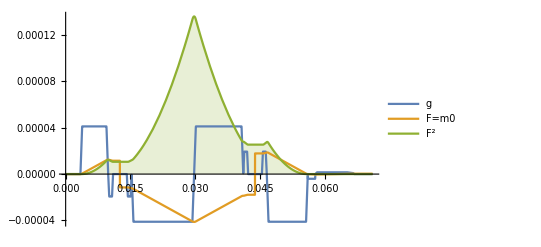
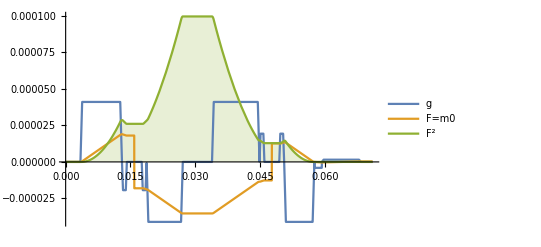
```mathematica
dirPlot=1;
{subs[Gread[t,dirPlot]/.t->TE]/.time2,subs[(γ*Fread[t,dirPlot]/.t->TE)]/.time2,subs[(γ*Fread[t,dirPlot]/.t->TE)^2]/.time2}//AbsoluteTiming;

(*Plot[{Gread[t,dirPlot]/.time2,ScaleDiagram*Fread[t,dirPlot]/.time2,8(100ScaleDiagram)^2*(Fread[t,dirPlot])^2/.time2},{t,0.*10^-6,71000.*10^-6},PlotRange->Full,Filling->{3->Axis},PlotLegends->{"g","F=m0","F^2"}]//AbsoluteTiming*)
(* TRSE:-Graphics- *)
(* TRSEadj:-Graphics-*)
```

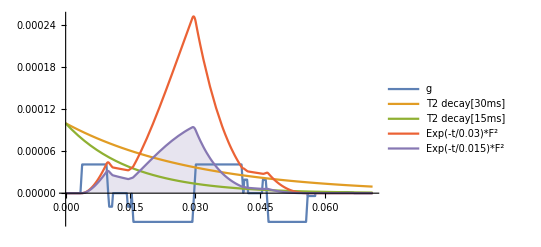
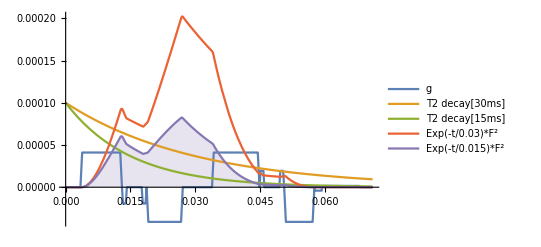
```mathematica
dirPlot=1;
(*Plot[{subs[Gread[t,dirPlot]]/.time2/.subamp[dirPlot],Exp[-t/0.030]*10^-4,Exp[-t/0.015]*10^-4,40(100ScaleDiagram)^2*subs[Exp[-t/0.03]*Fread[t,dirPlot]^2]/.time2/.subamp[dirPlot],40(100ScaleDiagram)^2*subs[Exp[-t/0.015]*Fread[t,dirPlot]^2]/.time2/.subamp[dirPlot]},{t,0.*10^-6,71000.*10^-6},PlotRange->Full,Filling->{5->Axis},PlotLegends->{"g","T2 decay[30ms]","T2 decay[15ms]","Exp(-t/0.03)*F^2","Exp(-t/0.015)*F^2"}]//AbsoluteTiming*)
(* TRSE: -Graphics-*)
(* TRSEadj: -Graphics-*)
```

```mathematica
PHASE;
dir=1;
While[dir<ndir+1,
AmpIntPhaseAtT1[dir]=subs[trap[Gpet,ϵ,Gpe,t-(t1-ϵ)]+ idtrap[δ1,ϵ,SignDelta[[1]]*Gdp,t2,T1]+idtrap[Crut,RampCrushers,-Gcp,t3,T1]]/.time2/.subamp[dir];

AmpIntPhaseAtT2[dir]=subs[-AmpIntPhaseAtT1[dir]+idtrap[Crut,RampCrushers,-Gcp,t3,T2]+idtrap[δ2,ϵ,SignDelta[[2]]*Gdp,t4,T2]+idtrap[δ11,ϵ,SignDelta[[3]]*Gdp,t6,T2]+idtrap[Crut,RampCrushers,Gcp,t7,T2]]/.time2/.subamp[dir];

Gphase[t_,dir]=subs[trap[Gpet,ϵ,Gpe,t-(t1-ϵ)]+trap[δ1,ϵ,SignDelta[[1]]*Gdp,t-t2]+trap[Crut,RampCrushers,-Gcp,t-t3]+trap[Crut,RampCrushers,-Gcp,t-(t4-(Crut+RampCrushers))]+trap[δ2,ϵ,SignDelta[[2]]*Gdp,t-t4]+trap[δ11,ϵ,SignDelta[[3]]*Gdp,t-t6]+trap[Crut,RampCrushers,Gcp,t-t7]+trap[Crut,RampCrushers,Gcp,t-(t8-(Crut+RampCrushers))]+trap[δ22,ϵ,SignDelta[[4]]*Gdp,t-t8]]/.time2/.subamp[dir];

Fphase[t_,dir]=subs[(1-UnitStep[t-T1])*(idtrap[Gpet,ϵ,Gpe,t1-ϵ,t]+idtrap[δ1,ϵ,SignDelta[[1]]*Gdp,t2,t]+idtrap[Crut,RampCrushers,-Gcp,t3,t])+
(UnitStep[t-T1]-UnitStep[t-T2])*(-AmpIntPhaseAtT1[dir]+idtrap[Crut,RampCrushers,-Gcp,t4-Crut,t])+
(1-UnitStep[t-T2])*(idtrap[δ2,ϵ,SignDelta[[2]]*Gdp,t4,t]+idtrap[δ11,ϵ,SignDelta[[3]]*Gdp,t6,t]+idtrap[Crut,RampCrushers,Gcp,t7,t])+UnitStep[t-T2]*(-AmpIntPhaseAtT2[dir]+idtrap[Crut,RampCrushers,Gcp,t8-Crut,t])+idtrap[δ22,ϵ,SignDelta[[4]]*Gdp,t8,t]]/.time2/.subamp[dir];
dir++];
dir=1;

dirPlot=1;
{subs[Gphase[t,dirPlot]/.t->TE]/.time2/.subamp[dirPlot],subs[γ*Fphase[t,dirPlot]/.t->TE]/.time2/.subamp[dirPlot],subs[(γ*Fphase[t,dirPlot]/.t->TE)^2]/.time2/.subamp[dirPlot]}//AbsoluteTiming;
```

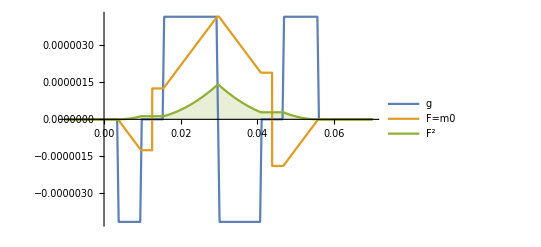
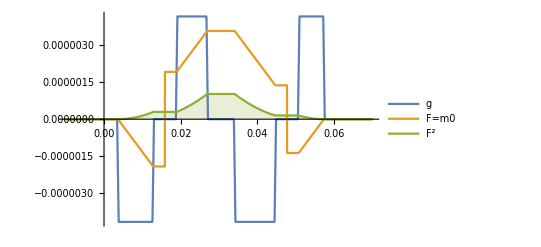
```mathematica
dirPlot=1;
(*Plot[{subs[Gphase[t,dirPlot]]/.time2/.subamp[dirPlot],ScaleDiagram*subs[Fphase[t,dirPlot]]/.time2/.subamp[dirPlot],8(100ScaleDiagram)^2*subs[(Fphase[t,dirPlot])^2]/.time2/.subamp[dirPlot]},{t,-10000.*10^-6,70000.*10^-6},PlotRange->Full,Filling->{3->Axis},PlotLegends->{"g","F=m0","F^2"}]//AbsoluteTiming*)
(* TRSE:-Graphics-*)
(* TRSEadj: -Graphics-*)
```

```mathematica
SLICE;
dir=1;
While[dir<ndir+1,
(* In TRSE the Flat top of Gsl180 starts when the duration of the crusher ends*)
(* In TRSE adjusted the Flat top of Gsl180 starts when the total time of the crusher ends*)
If[TRSE==1,
AmpIntSliceAtT1[dir]=subs[idtrap[Gsl90t,ϵ,Gsl90,t1,T1]/2.+idtrap[Gsrft,ϵ,Gsrf,t1,T1]+idtrap[δ1,ϵ,SignDelta[[1]]*Gds,t2,T1]+idtrap[Crut,RampCrushers,-Gcs,t3,T1]+idtrap[Gsl180t,RampGsl180,Gsl180,t3,T1]]/.time2/.subamp[dir];

AmpIntSliceAtT2[dir]=subs[-AmpIntSliceAtT1[dir]+idtrap[Gsl180t,RampGsl180,Gsl180,T1,T2]+idtrap[Crut,RampCrushers,-Gcs,T1,T2]+idtrap[δ2,ϵ,SignDelta[[2]]*Gds,t4,T2]+idtrap[δ11,ϵ,SignDelta[[3]]*Gds,t6,T2]+idtrap[Crut,RampCrushers,Gcs,t7,T2]+idtrap[Gsl180t,RampGsl180,Gsl180,t7,T2]]/.time2/.subamp[dir];

Gslice[t_,dir]= subs[trap[Gsl90t,ϵ,Gsl90,t+t1]+trap[Gsrft,ϵ,Gsrf,t-t1]+trap[δ1,ϵ,SignDelta[[1]]*Gds,t-t2]+trap[Crut,RampCrushers,-Gcs,t-t3]+trap[Gsl180t,RampGsl180,Gsl180,t-t3]+trap[Crut,RampCrushers,-Gcs,t-(t4-(Crut+RampCrushers))]+trap[δ2,ϵ,SignDelta[[2]]*Gds,t-t4]+trap[δ11,ϵ,SignDelta[[3]]*Gds,t-t6]+trap[Crut,RampCrushers,Gcs,t-t7]+trap[Gsl180t,RampGsl180,Gsl180,t-t7]+trap[Crut,RampCrushers,Gcs,t-(t8-(Crut+RampCrushers))]+trap[δ22,ϵ,SignDelta[[4]]*Gds,t-t8]]/.time2/.subamp[dir];

Fslice[t_,dir]=subs[(1-UnitStep[t-t1])*idtrap[Gsl90t,ϵ,Gsl90,t1,t+t1]/2.+UnitStep[t-t1]*(idtrap[Gsl90t,ϵ,Gsl90,t1,t+t1]/2.+idtrap[Gsrft,ϵ,Gsrf,t1,t])+
(1-UnitStep[t-T1])*(idtrap[δ1,ϵ,SignDelta[[1]]*Gds,t2,t]+idtrap[Crut,RampCrushers,-Gcs,t3,t]+idtrap[Gsl180t,RampGsl180,Gsl180,t3,t])+
(UnitStep[t-T1]-UnitStep[t-T2])*(-AmpIntSliceAtT1[dir]+idtrap[Gsl180t,RampGsl180,Gsl180,t3,t]-idtrap[Gsl180t,RampGsl180,Gsl180,t3,T1]+idtrap[Crut,RampCrushers,-Gcs,t4-(Crut+RampCrushers),t])+
(1-UnitStep[t-T2])*(idtrap[δ2,ϵ,SignDelta[[2]]*Gds,t4,t]+idtrap[δ11,ϵ,SignDelta[[3]]*Gds,t6,t]+idtrap[Crut,RampCrushers,Gcs,t7,t]+idtrap[Gsl180t,RampGsl180,Gsl180,t7,t])+UnitStep[t-T2]*(-AmpIntSliceAtT2[dir]+idtrap[Gsl180t,RampGsl180,Gsl180,t7,t]+idtrap[Crut,RampCrushers,Gcs,t8-(Crut+RampCrushers),t])+idtrap[δ22,ϵ,SignDelta[[4]]*Gds,t8,t]]/.time2/.subamp[dir];
,
AmpIntSliceAtT1[dir]=subs[idtrap[Gsl90t,ϵ,Gsl90,t1,T1]/2.+idtrap[Gsrft,ϵ,Gsrf,t1,T1]+idtrap[δ1,ϵ,SignDelta[[1]]*Gds,t2,T1]+idtrap[Crut,RampCrushers,-Gcs,t3,T1]+idtrap[Gsl180t,RampGsl180,Gsl180,(t3+Crut+RampCrushers-RampGsl180),T1]]/.time2/.subamp[dir];

AmpIntSliceAtT2[dir]=subs[-AmpIntSliceAtT1[dir]+idtrap[Gsl180t,RampGsl180,Gsl180,(t3+Crut+RampCrushers-RampGsl180),T2]+idtrap[Crut,RampCrushers,-Gcs,t3,T2]+idtrap[δ2,ϵ,SignDelta[[2]]*Gds,t4,T2]+idtrap[δ11,ϵ,SignDelta[[3]]*Gds,t6,T2]+idtrap[Crut,RampCrushers,Gcs,(t7+Crut+RampCrushers-RampGsl180),T2]+idtrap[Gsl180t,RampGsl180,Gsl180,t7,T2]]/.time2/.subamp[dir];

Gslice[t_,dir]= subs[trap[Gsl90t,ϵ,Gsl90,t+t1]+trap[Gsrft,ϵ,Gsrf,t-t1]+trap[δ1,ϵ,SignDelta[[1]]*Gds,t-t2]+trap[Crut,RampCrushers,-Gcs,t-t3]+trap[Gsl180t,RampGsl180,Gsl180,t-(t3+Crut+RampCrushers-RampGsl180)]+trap[Crut,RampCrushers,-Gcs,t-(t4-(Crut+RampCrushers))]+trap[δ2,ϵ,SignDelta[[2]]*Gds,t-t4]+trap[δ11,ϵ,SignDelta[[3]]*Gds,t-t6]+trap[Crut,RampCrushers,Gcs,t-t7]+trap[Gsl180t,RampGsl180,Gsl180,t-(t7+Crut+RampCrushers-RampGsl180)]+trap[Crut,RampCrushers,Gcs,t-(t8-(Crut+RampCrushers))]+trap[δ22,ϵ,SignDelta[[4]]*Gds,t-t8]]/.time2/.subamp[dir];

Fslice[t_,dir]=subs[(1-UnitStep[t-t1])*(idtrap[Gsl90t,ϵ,Gsl90,t1,t+t1]/2.)+UnitStep[t-t1]*(idtrap[Gsl90t,ϵ,Gsl90,t1,t+t1]/2.+idtrap[Gsrft,ϵ,Gsrf,t1,t])+
(1-UnitStep[t-T1])*(idtrap[δ1,ϵ,SignDelta[[1]]*Gds,t2,t]+idtrap[Crut,RampCrushers,-Gcs,t3,t]+idtrap[Gsl180t,RampGsl180,Gsl180,(t3+Crut+RampCrushers-RampGsl180),t])+
(UnitStep[t-T1]-UnitStep[t-T2])*(-AmpIntSliceAtT1[dir]+idtrap[Gsl180t,RampGsl180,Gsl180,(t3+Crut+RampCrushers-RampGsl180),t]-idtrap[Gsl180t,RampGsl180,Gsl180,(t3+Crut+RampCrushers-RampGsl180),T1]+idtrap[Crut,RampCrushers,-Gcs,t4-(Crut+RampCrushers),t])+
(1-UnitStep[t-T2])*(idtrap[δ2,ϵ,SignDelta[[2]]*Gds,t4,t]+idtrap[δ11,ϵ,SignDelta[[3]]*Gds,t6,t]+idtrap[Crut,RampCrushers,Gcs,t7,t]+idtrap[Gsl180t,RampGsl180,Gsl180,(t7+Crut+RampCrushers-RampGsl180),t])+UnitStep[t-T2]*(-AmpIntSliceAtT2[dir]+idtrap[Gsl180t,RampGsl180,Gsl180,(t7+Crut+RampCrushers-RampGsl180),t]+idtrap[Crut,RampCrushers,Gcs,t8-(Crut+RampCrushers),t])+idtrap[δ22,ϵ,SignDelta[[4]]*Gds,t8,t]]/.time2/.subamp[dir];
];
dir++];
dir=1;

dirPlot=3;
{subs[Gslice[t,dirPlot]/.t->TE]/.time2/.subamp[dirPlot],subs[γ*Fslice[t,dirPlot]/.t->TE]/.time2/.subamp[dirPlot],subs[(γ*Fslice[t,dirPlot]/.t->TE)^2]/.time2/.subamp[dirPlot]}//AbsoluteTiming;
```

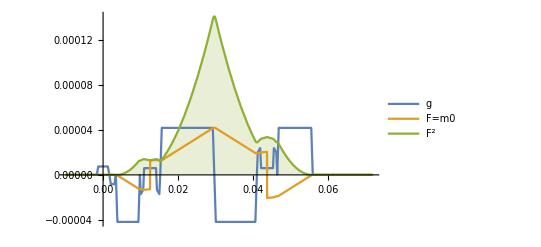
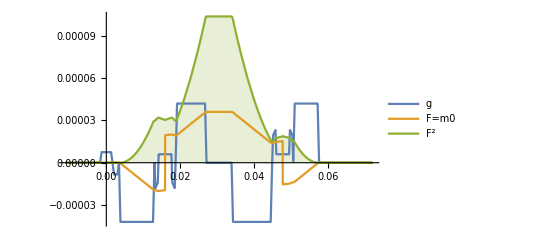
```mathematica
(*Plot[{subs[Gslice[t,dirPlot]]/.time2/.subamp[dirPlot],ScaleDiagram*subs[Fslice[t,dirPlot]]/.time2/.subamp[dirPlot],8(100ScaleDiagram)^2*subs[(Fslice[t,dirPlot])^2]/.time2/.subamp[dirPlot]},{t,-11000.*10^-6,72000.*10^-6},PlotRange->Full,Filling->{3->Axis},PlotLegends->{"g","F=m0","F^2"}]//AbsoluteTiming*)
(* TRSE:-Graphics-*)
(* TRSEadj: -Graphics-*)
```

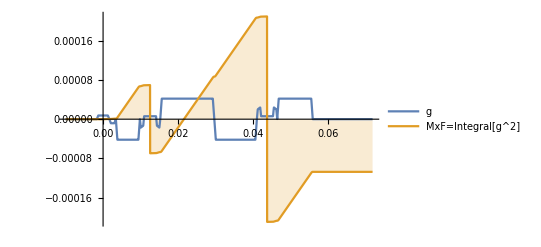
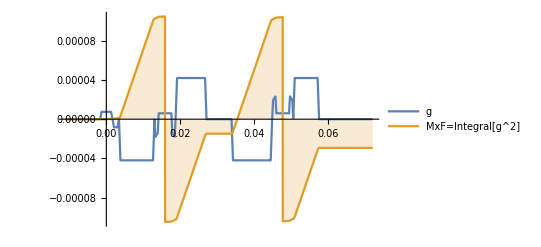
```mathematica
"Maxwell gradient moment= integral(g^2)";
dir=1;
While[dir<ndir+1,
AmpMxIntSliceAtT1[dir]=subs[ idtrap[Gsl90t,ϵ,Gsl90^2,t1,T1]/2+idtrap[Gsrft,ϵ,Gsrf^2,t1,T1]+idtrap[δ1,ϵ,(SignDelta[[1]]*Gds)^2,t2,T1]+idtrap[Crut,RampCrushers,(-Gcs)^2,t3,T1]+idtrap[Gsl180t,RampGsl180,Gsl180^2,t3,T1]]/.time2/.subamp[dir];

AmpMxIntSliceAtT2[dir]=subs[-AmpMxIntSliceAtT1[dir]+idtrap[Gsl180t,RampGsl180,Gsl180^2,t3,T1]+idtrap[Crut,RampCrushers,(-Gcs)^2,t4-(Crut+RampCrushers),T2]+idtrap[δ2,ϵ,(SignDelta[[2]]*Gds)^2,t4,T2]+idtrap[δ11,ϵ,(SignDelta[[3]]*Gds)^2,t6,T2]+idtrap[Crut,RampCrushers,Gcs^2,t7,T2]+idtrap[Gsl180t,RampGsl180,Gsl180^2,t7,T2]]/.time2/.subamp[dir];

MxFslice[t_,dir]=(1-UnitStep[t-t1])*idtrap[Gsl90t,ϵ,Gsl90^2,t1,t+t1]/2.+
(1-UnitStep[t-T1])*(idtrap[Gsl90t,ϵ,Gsl90^2,t1,t+t1]/2.+idtrap[Gsrft,ϵ,Gsrf^2,t1,t]+idtrap[δ1,ϵ,(SignDelta[[1]]*Gds)^2,t2,t]+idtrap[Crut,RampCrushers,(-Gcs)^2,t3,t]+idtrap[Gsl180t,RampGsl180,Gsl180^2,t3,t])+(UnitStep[t-T1]-UnitStep[t-T2])*(-AmpMxIntSliceAtT1[dir]+idtrap[Gsl180t,RampGsl180,Gsl180^2,t3,t]-idtrap[Gsl180t,RampGsl180,Gsl180^2,t3,T1]+idtrap[Crut,RampCrushers,(-Gcs)^2,t4-(Crut+RampCrushers),t]+idtrap[δ2,ϵ,(SignDelta[[2]]*Gds)^2,t4,t]+idtrap[δ11,ϵ,(SignDelta[[3]]*Gds)^2,t6,t]+idtrap[Crut,RampCrushers,Gcs^2,t7,t]+idtrap[Gsl180t,RampGsl180,Gsl180^2,t7,t])+
UnitStep[t-T2]*(-AmpMxIntSliceAtT2[dir]+
idtrap[Gsl180t,RampGsl180,Gsl180^2,t7,t]-idtrap[Gsl180t,RampGsl180,Gsl180^2,t7,T2]+idtrap[Crut,RampCrushers,Gcs^2,t8-(Crut+RampCrushers),t])+idtrap[δ22,ϵ,(SignDelta[[4]]*Gds)^2,t8,t];
dir++];
dir=1;

dirPlot=3;
{subs[Gslice[t,dirPlot]/.t->TE]/.time2/.subamp[dirPlot],subs[(MxFslice[t,dirPlot]/.t->TE)]/.time2/.subamp[dirPlot]};
(*Plot[{subs[Gslice[t,dirPlot]]/.time2/.subamp[dirPlot],(50ScaleDiagram)^2*subs[MxFslice[t,dirPlot]]/.time2/.subamp[dirPlot]},{t,-11000.*10^-6,72000.*10^-6},PlotRange->Full,Filling->{2->Axis},PlotLegends->{"g","MxF=Integral[g^2]"}]//AbsoluteTiming*)
(* TRSE: -Graphics-*)

(* TRSEadj: -Graphics-*)
```

```mathematica
integral(integral);
```

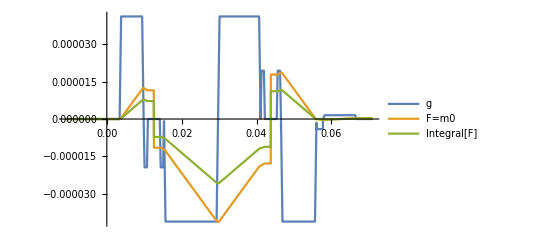
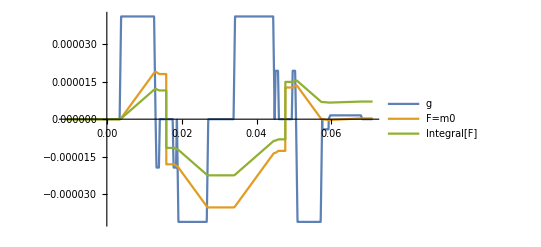
```mathematica
i2dtrap[DurationGrad_,RampTime_,AmpGrad_,ll_,ul_,a_,b_]=Simplify[Refine[FiInt[idtrap[DurationGrad,RampTime,amp,ll,ul],a,b],Assumptions->{wid>0.,a≥0.,b>a,b>0.,a<ul<b,ll≥0.,RampTime>0.,ul>0.,AmpGrad≥0.,wid>RampTime}]]/.wid->DurationGrad/.amp->AmpGrad;

READ;
dir=1;
While[dir<ndir+1,
Amp2IntReadAtT1[dir]=subs[ i2dtrap[δ1,ϵ,SignDelta[[1]]*Gdr,t2,T1,0,TE]+i2dtrap[Crut,RampCrushers,-Gcr,t3,T1,0,TE]]/.time2/.subamp[dir];

Amp2IntReadAtT2[dir]=subs[Abs[Amp2IntReadAtT1[dir]]+Abs[i2dtrap[Crut,RampCrushers,-Gcr,t3,T2,0,TE]+i2dtrap[δ2,ϵ,SignDelta[[2]]*Gdr,t4,T2,0,TE]+i2dtrap[δ11,ϵ,SignDelta[[3]]*Gdr,t6,T2,0,TE]+i2dtrap[Crut,RampCrushers,Gcr,t7,T2,0,TE]]]/.time2/.subamp[dir];

IntFread[t_,dir]=(1-UnitStep[t-T1])*(i2dtrap[δ1,ϵ,SignDelta[[1]]*Gdr,t2,t,0,TE]+i2dtrap[Crut,RampCrushers,-Gcr,t3,t,0,TE])+
(UnitStep[t-T1]-UnitStep[t-T2])*(-Amp2IntReadAtT1[dir]+i2dtrap[Crut,RampCrushers,-Gcr,t4-Crut,t,0,TE])+
(1-UnitStep[t-T2])*(i2dtrap[δ2,ϵ,SignDelta[[2]]*Gdr,t4,t,0,TE]+i2dtrap[δ11,ϵ,SignDelta[[3]]*Gdr,t6,t,0,TE]+i2dtrap[Crut,RampCrushers,Gcr,t7,t,0,TE])+UnitStep[t-T2]*(-Sign[-Amp2IntReadAtT1[dir]]*Amp2IntReadAtT2[dir]+i2dtrap[Crut,RampCrushers,Gcr,t8-Crut,t,0,TE])+i2dtrap[δ22,ϵ,SignDelta[[4]]*Gdr,t8,t,0,TE]+i2dtrap[Grdpt,ϵ,Grdp,t9,t,0,TE]+i2dtrap[Grot,ϵ,Gro,t10,t,0,TE];
dir++];
dir=1;

dirPlot=1;
(*Plot[{subs[Gread[t,dirPlot]]/.time2/.subamp[dirPlot],ScaleDiagram*subs[Fread[t,dirPlot]]/.time2/.subamp[dirPlot],10ScaleDiagram*subs[IntFread[t,dirPlot]]/.time2/.subamp[dirPlot]},{t,-11000*10^-6,71000*10^-6},PlotRange->Full,PlotLegends->{"g","F=m0","Integral[F]"}]*)
(* TRSE:-Graphics-*)
(* TRSEadj: -Graphics-*)
```

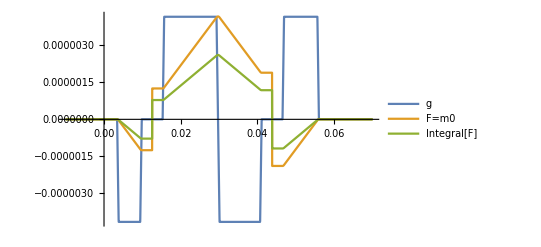
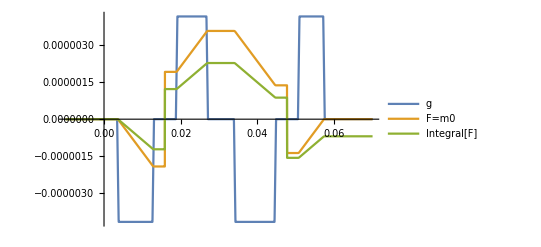
```mathematica
PHASE;
dir=1;
While[dir<ndir+1,
Amp2IntPhaseAtT1[dir]=subs[i2dtrap[Gpet,RampGpe,Gpe,t1,T1,0,TE]+ i2dtrap[δ1,ϵ,SignDelta[[1]]*Gdp,t2,T1,0,TE]+i2dtrap[Crut,RampCrushers,-Gcp,t3,T1,0,TE]]/.time2/.subamp[dir];

Amp2IntPhaseAtT2[dir]=subs[Abs[Amp2IntPhaseAtT1[dir]]+Abs[i2dtrap[Crut,RampCrushers,-Gcp,t3,T2,0,TE]+i2dtrap[δ2,ϵ,SignDelta[[2]]*Gdp,t4,T2,0,TE]+i2dtrap[δ11,ϵ,SignDelta[[3]]*Gdp,t6,T2,0,TE]+i2dtrap[Crut,RampCrushers,Gcp,t7,T2,0,TE]]]/.time2/.subamp[dir];

IntFphase[t_,dir]=(1-UnitStep[t-T1])*(i2dtrap[Gpet,RampGpe,Gpe,t1,t,0,TE]+i2dtrap[δ1,ϵ,SignDelta[[1]]*Gdp,t2,t,0,TE]+i2dtrap[Crut,RampCrushers,-Gcp,t3,t,0,TE])+
(UnitStep[t-T1]-UnitStep[t-T2])*(-Amp2IntPhaseAtT1[dir]+i2dtrap[Crut,RampCrushers,-Gcp,t4-Crut,t,0,TE])+
(1-UnitStep[t-T2])*(i2dtrap[δ2,ϵ,SignDelta[[2]]*Gdp,t4,t,0,TE]+i2dtrap[δ11,ϵ,SignDelta[[3]]*Gdp,t6,t,0,TE]+i2dtrap[Crut,RampCrushers,Gcp,t7,t,0,TE])+UnitStep[t-T2]*(-Sign[-Amp2IntPhaseAtT1[dir]]*Amp2IntPhaseAtT2[dir]+i2dtrap[Crut,RampCrushers,Gcp,t8-Crut,t,0,TE])+i2dtrap[δ22,ϵ,SignDelta[[4]]*Gdp,t8,t,0,TE];
dir++];
dir=1;

dirPlot=1;
(*Plot[{subs[Gphase[t,dirPlot]]/.time2/.subamp[dirPlot],ScaleDiagram*subs[Fphase[t,dirPlot]]/.time2/.subamp[dirPlot],10ScaleDiagram*subs[IntFphase[t,dirPlot]]/.time2/.subamp[dirPlot]},{t,-10000*10^-6,70000*10^-6},PlotRange->Full,PlotLegends->{"g","F=m0","Integral[F]"}]*)
(* TRSE:-Graphics-*)
(* TRSEadj: -Graphics-*)
```

```mathematica
SLICE;
dir=1;
While[dir<ndir+1,
Amp2IntSliceAtT1[dir]=subs[ i2dtrap[Gsl90t,ϵ,Gsl90,t1,T1,0,TE]/2.+i2dtrap[Gsrft,ϵ,Gsrf,t1,T1,0,TE]+i2dtrap[δ1,ϵ,SignDelta[[1]]*Gds,t2,T1,0,TE]+i2dtrap[Crut,RampCrushers,-Gcs,t3,T1,0,TE]+i2dtrap[Gsl180t,RampGsl180,Gsl180,t3,TE,0,TE]/2.]/.time2/.subamp[dir];

Amp2IntSliceAtT2[dir]=subs[Abs[Amp2IntSliceAtT1[dir]]+Abs[i2dtrap[Gsl180t,RampGsl180,Gsl180,t3,TE,0,TE]/2.+i2dtrap[Crut,RampCrushers,-Gcs,t3,T2,0,TE]+i2dtrap[δ2,ϵ,SignDelta[[2]]*Gds,t4,T2,0,TE]+i2dtrap[δ11,ϵ,SignDelta[[3]]*Gds,t6,T2,0,TE]+i2dtrap[Crut,RampCrushers,Gcs,t3,T2,0,TE]+i2dtrap[Gsl180t,RampGsl180,Gsl180,t7,T2,0,TE]]]/.time2/.subamp[dir];

IntFslice[t_,dir]=(1-UnitStep[t-t1])*i2dtrap[Gsl90t,ϵ,Gsl90,t1,t+t1,0,TE]/2.+UnitStep[t-t1]*(i2dtrap[Gsl90t,ϵ,Gsl90,t1,t+t1,0,TE]/2.+i2dtrap[Gsrft,ϵ,Gsrf,t1,t,0,TE])+
(1-UnitStep[t-T1])*(i2dtrap[δ1,ϵ,SignDelta[[1]]*Gds,t2,t,0,TE]+i2dtrap[Crut,RampCrushers,-Gcs,t3,t,0,TE]+i2dtrap[Gsl180t,RampGsl180,Gsl180,t3,t,0,TE])+
(UnitStep[t-T1]-UnitStep[t-T2])*(-Amp2IntSliceAtT1[dir]+i2dtrap[Gsl180t,RampGsl180,Gsl180,t3,t,0,TE]+i2dtrap[Crut,RampCrushers,-Gcs,t4-Crut,t,0,TE])+
(1-UnitStep[t-T2])*(i2dtrap[δ2,ϵ,SignDelta[[2]]*Gds,t4,t,0,TE]+i2dtrap[δ11,ϵ,SignDelta[[3]]*Gds,t6,t,0,TE]+i2dtrap[Crut,RampCrushers,Gcs,t7,t,0,TE]+i2dtrap[Gsl180t,RampGsl180,Gsl180,t7,t,0,TE])+UnitStep[t-T2]*(-Sign[-Amp2IntSliceAtT1[dir]]*Amp2IntSliceAtT2[dir]+i2dtrap[Gsl180t,RampGsl180,Gsl180,t7,t,0,TE]-i2dtrap[Gsl180t,RampGsl180,Gsl180,t7,T2,0,TE]+i2dtrap[Crut,RampCrushers,Gcs,t8-Crut,t,0,TE])+i2dtrap[δ22,ϵ,SignDelta[[4]]*Gds,t8,t,0,TE];
dir++];
dir=1;
```

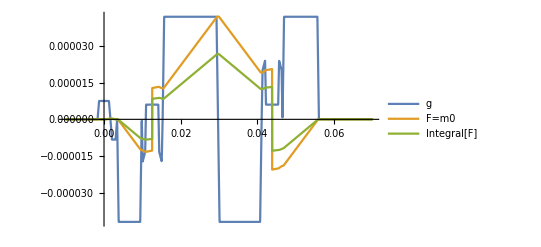
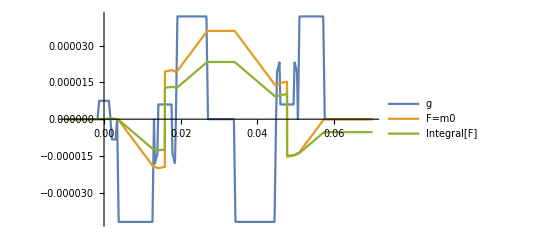
```mathematica
dirPlot=3;
(*Plot[{subs[Gslice[t,dirPlot]]/.time2/.subamp[dirPlot],ScaleDiagram*subs[Fslice[t,dirPlot]]/.time2/.subamp[dirPlot],10ScaleDiagram*subs[IntFslice[t,dirPlot]]/.time2/.subamp[dirPlot]},{t,-10000*10^-6,70000*10^-6},PlotRange->Full,PlotLegends->{"g","F=m0","Integral[F]"}]*)
(* TRSE:-Graphics-*)
(* TRSEadj: -Graphics-*)
```

```mathematica
integral[integral^2];
```

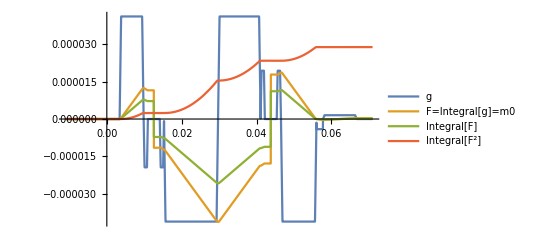
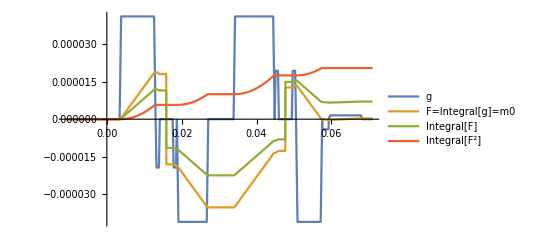
```mathematica
iSqidtrap[DurationGrad_,RampTime_,AmpGrad_,ll_,ul_,a_,b_]=Simplify[Refine[FiInt[(idtrap[DurationGrad,RampTime,amp,ll,ul])^2,a,b],Assumptions->{wid>0.,a≥0.,b>a,b>0.,a<ul<b,ll≥0.,RampTime>0.,ul>0.,AmpGrad≥0.,wid>RampTime}]]/.wid->DurationGrad/.amp->AmpGrad;
dir=1;
While[dir<ndir+1,
AmpIntSqIntReadAtT1[dir]=subs[ iSqidtrap[δ1,ϵ,SignDelta[[1]]*Gdr,t2,T1,0,TE]+iSqidtrap[Crut,RampCrushers,-Gcr,t3,T1,0,TE]]/.time2/.subamp[dir];

AmpIntSqIntReadAtT2[dir]=subs[Abs[AmpIntSqIntReadAtT1[dir]]+Abs[iSqidtrap[Crut,RampCrushers,-Gcr,t3,T2,0,TE]+iSqidtrap[δ2,ϵ,SignDelta[[2]]*Gdr,t4,T2,0,TE]+iSqidtrap[δ11,ϵ,SignDelta[[3]]*Gdr,t6,T2,0,TE]+iSqidtrap[Crut,RampCrushers,Gcr,t7,T2,0,TE]]]/.time2/.subamp[dir];

IntSqFread[t_,dir]=
iSqidtrap[δ1,ϵ,SignDelta[[1]]*Gdr,t2,t,0,TE]+iSqidtrap[Crut,RampCrushers,-Gcr,t3,t,0,TE]+
(UnitStep[t-T1]-UnitStep[t-T2])*(iSqidtrap[Crut,RampCrushers,-Gcr,t4-Crut,t,0,TE])+
iSqidtrap[δ2,ϵ,SignDelta[[2]]*Gdr,t4,t,0,TE]+iSqidtrap[δ11,ϵ,SignDelta[[3]]*Gdr,t6,t,0,TE]+iSqidtrap[Crut,RampCrushers,Gcr,t7,t,0,TE]+iSqidtrap[Crut,RampCrushers,Gcr,t8-Crut,t,0,TE]+iSqidtrap[δ22,ϵ,SignDelta[[4]]*Gdr,t8,t,0,TE]+iSqidtrap[Grdpt,RampGrdp,Grdp,t9,t,0,TE]+iSqidtrap[Grot,ϵ,Gro,t10,t,0,TE];
dir++];
dir=1;

dirPlot=1;
(*Plot[{subs[Gread[t,dirPlot]]/.time2/.subamp[dirPlot],ScaleDiagram*subs[Fread[t,dirPlot]]/.time2/.subamp[dirPlot],10ScaleDiagram*subs[IntFread[t,dirPlot]]/.time2/.subamp[dirPlot],(500ScaleDiagram)^2*subs[IntSqFread[t,dirPlot]]/.time2/.subamp[dirPlot]},{t,-11000*10^-6,71000*10^-6},PlotRange->Full,PlotLegends->{"g","F=Integral[g]=m0","Integral[F]","Integral[F^2]"}]*)
(* TRSE: -Graphics-*)
(* TRSEadj: -Graphics-*)
```

```mathematica
PHASE;
dir=1;
While[dir<ndir+1,
AmpIntSqIntPhaseAtT1[dir]=subs[ iSqidtrap[Gpet,ϵ,Gpe,t1,T1,0,TE]+iSqidtrap[δ1,ϵ,SignDelta[[1]]*Gdp,t2,T1,0,TE]+iSqidtrap[Crut,RampCrushers,-Gcp,t3,T1,0,TE]]/.time2/.subamp[dir];

AmpIntSqIntPhaseAtT2[dir]=subs[Abs[AmpIntSqIntPhaseAtT1[dir]]+Abs[iSqidtrap[Crut,RampCrushers,-Gcp,t3,T2,0,TE]+iSqidtrap[δ2,ϵ,SignDelta[[2]]*Gdp,t4,T2,0,TE]+iSqidtrap[δ11,ϵ,SignDelta[[3]]*Gdp,t6,T2,0,TE]+iSqidtrap[Crut,RampCrushers,Gcp,t7,T2,0,TE]]]/.time2/.subamp[dir];

IntSqFphase[t_,dir]=iSqidtrap[Gpet,ϵ,Gpe,t1,t,0,TE]+
iSqidtrap[δ1,ϵ,SignDelta[[1]]*Gdp,t2,t,0,TE]+iSqidtrap[Crut,RampCrushers,-Gcp,t3,t,0,TE]+
(UnitStep[t-T1]-UnitStep[t-T2])*iSqidtrap[Crut,RampCrushers,-Gcp,t4-Crut,t,0,TE]+
iSqidtrap[δ2,ϵ,SignDelta[[2]]*Gdp,t4,t,0,TE]+iSqidtrap[δ11,ϵ,SignDelta[[3]]*Gdp,t6,t,0,TE]+iSqidtrap[Crut,RampCrushers,Gcp,t7,t,0,TE]+iSqidtrap[Crut,RampCrushers,Gcp,t8-Crut,t,0,TE]+iSqidtrap[δ22,ϵ,SignDelta[[4]]*Gdp,t8,t,0,TE];
dir++];
dir=1;
```

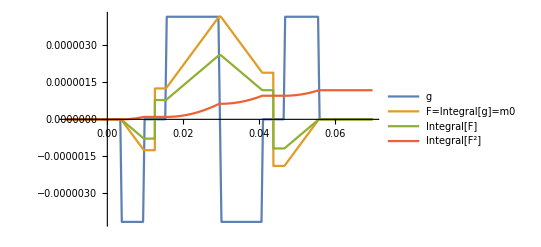
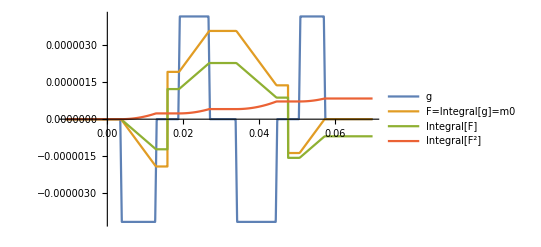
```mathematica
dirPlot=1;
(*Plot[{subs[Gphase[t,dirPlot]]/.time2/.subamp[dirPlot],ScaleDiagram*subs[Fphase[t,dirPlot]]/.time2/.subamp[dirPlot],10ScaleDiagram*subs[IntFphase[t,dirPlot]]/.time2/.subamp[dirPlot],(1000ScaleDiagram)^2*subs[IntSqFphase[t,dirPlot]]/.time2/.subamp[dirPlot]},{t,-11000*10^-6,70000*10^-6},PlotRange->Full,PlotLegends->{"g","F=Integral[g]=m0","Integral[F]","Integral[F^2]"}]*)
(* TRSE: -Graphics-*)
(* TRSEadj: -Graphics-*)
```

```mathematica
SLICE;
dir=1;
While[dir<ndir+1,
AmpIntSqIntSliceAtT1[dir]=subs[ iSqidtrap[Gsl90t,ϵ,Gsl90,t1,T1,0,TE]/2.+iSqidtrap[Gsrft,ϵ,Gsrf,t1,T1,0,TE]+iSqidtrap[δ1,ϵ,SignDelta[[1]]*Gds,t2,T1,0,TE]+iSqidtrap[Crut,RampCrushers,-Gcs,t3,T1,0,TE]+iSqidtrap[Gsl180t,RampGsl180,Gsl180,t3,TE,0,TE]/2.]/.time2/.subamp[dir];

AmpIntSqIntSliceAtT2[dir]=subs[Abs[AmpIntSqIntSliceAtT1[dir]]+Abs[iSqidtrap[Gsl180t,RampGsl180,Gsl180,t3,TE,0,TE]/2.+iSqidtrap[Crut,RampCrushers,-Gcs,t3,T2,0,TE]+iSqidtrap[δ2,ϵ,SignDelta[[2]]*Gds,t4,T2,0,TE]+iSqidtrap[δ11,ϵ,SignDelta[[3]]*Gds,t6,T2,0,TE]+iSqidtrap[Crut,RampCrushers,Gcs,t3,T2,0,TE]+iSqidtrap[Gsl180t,RampGsl180,Gsl180,t7,T2,0,TE]]]/.time2/.subamp[dir];

IntSqFslice[t_,dir]=(1-UnitStep[t-t1])*iSqidtrap[Gsl90t,ϵ,Gsl90,t1,t+t1,0,TE]/2.+(iSqidtrap[Gsl90t,ϵ,Gsl90,t1,t+t1,0,TE]/2.+iSqidtrap[Gsrft,ϵ,Gsrf,t1,t,0,TE])+
(iSqidtrap[δ1,ϵ,SignDelta[[1]]*Gds,t2,t,0,TE]+iSqidtrap[Crut,RampCrushers,-Gcs,t3,t,0,TE]+iSqidtrap[Gsl180t,RampGsl180,Gsl180,t3,t,0,TE])+
(UnitStep[t-T1]-UnitStep[t-T2])*(iSqidtrap[Gsl180t,RampGsl180,Gsl180,t3,t,0,TE]+iSqidtrap[Crut,RampCrushers,-Gcs,t4-Crut,t,0,TE])+
(iSqidtrap[δ2,ϵ,SignDelta[[2]]*Gds,t4,t,0,TE]+iSqidtrap[δ11,ϵ,SignDelta[[3]]*Gds,t6,t,0,TE]+iSqidtrap[Crut,RampCrushers,Gcs,t7,t,0,TE]+iSqidtrap[Gsl180t,RampGsl180,Gsl180,t7,t,0,TE])+iSqidtrap[Gsl180t,RampGsl180,Gsl180,t7,t,0,TE]-iSqidtrap[Gsl180t,RampGsl180,Gsl180,t7,T2,0,TE]+iSqidtrap[Crut,RampCrushers,Gcs,t8-Crut,t,0,TE]+iSqidtrap[δ22,ϵ,SignDelta[[4]]*Gds,t8,t,0,TE];
dir++];
dir=1;
```

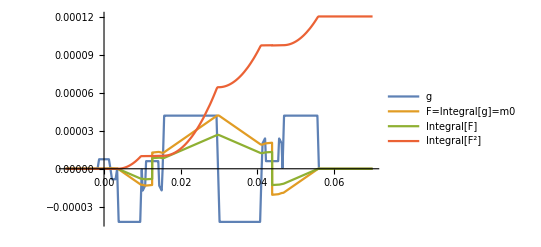
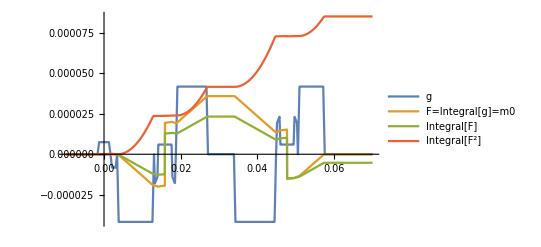
```mathematica
dirPlot=3;
(*Plot[{subs[Gslice[t,dirPlot]]/.time2/.subamp[dirPlot],ScaleDiagram*subs[Fslice[t,dirPlot]]/.time2/.subamp[dirPlot],10ScaleDiagram*subs[IntFslice[t,dirPlot]]/.time2/.subamp[dirPlot],(1000ScaleDiagram)^2*subs[IntSqFslice[t,dirPlot]]/.time2/.subamp[dirPlot]},{t,-10000*10^-6,70000*10^-6},PlotRange->Full,PlotLegends->{"g","F=Integral[g]=m0","Integral[F]","Integral[F^2]"}]*)
(* TRSE: -Graphics-*)
(* TRSEadj: -Graphics-*)
```

```mathematica
"Bmatrix calculation";
(*set SignDelta={1.,1.,-1.,-1.};*)
```

```mathematica
f1 and f2 calculation;
dir=1;
While[dir<ndir+1,
(F[t_,dir]={{Fread[t,dir]},{Fphase[t,dir]},{Fslice[t,dir]}})//MatrixForm;

f1read[dir]=Fread[t,dir]/.t->T1 ;
f1phase[dir]=Fphase[t,dir]/.t->T1 ;
f1slice[dir]=Fslice[t,dir]/.t->T1 ;
(f1[dir]={{f1read[dir]},{f1phase[dir]},{f1slice[dir]}})//MatrixForm;

f2read[dir]=Fread[t,dir]/.t->T2 ;
f2phase[dir]=Fphase[t, dir]/.t->T2 ;
f2slice[dir]=Fslice[t,dir]/.t->T2 ;
(f2[dir]={{f2read[dir]},{f2phase[dir]},{f2slice[dir]}})//MatrixForm;
dir++];
dir=1;
```

```mathematica
b calculation;
(* with b = γ^2*Integral[ Transpose[F-( (ζ-1)f1 + (β-1)f2].[F-( (ζ-1)f1 + (β-1)f2],{t,0,TE}] with ζ=1 at t<T1 and ζ=-1 at t>T1; β=1 at t<T2 and β=-1 at t>T2 *)
dir=1;
While[dir<ndir+1,
b1v[dir]=NIntegrate[F[t,dir].Transpose[F[t,dir]],{t, 0,T1}];
b2v[dir]=NIntegrate[(F[t,dir]-2f1[dir]).Transpose[F[t,dir]-2f1[dir]],{t,T1,T2}];
b3v[dir]=NIntegrate[(F[t,dir]-2f1[dir]-2f2[dir]).Transpose[F[t,dir]-2f1[dir]-2f2[dir]],{t,T2, N[TE/.time1]}];
dir++];
dir=1;
```

```mathematica
bTensor=Reap[Do[Sow[γ^2*(b1v[dir]+b2v[dir]+b3v[dir])],{dir,1,ndir}]][[2]]//MatrixForm;
bTrace=Transpose[Reap[Do[Sow[Tr[bTensor[[1,1,dir]]]],{dir,1,ndir}]][[2]]];
Mean[bTrace]; (* 749.86 *)
StandardDeviation[bTrace]; (* 32.33 *)
Bmatrix=Reap[Do[Sow[ {bTensor[[1,1,dir,1,1]], bTensor[[1,1,dir,2,2]], bTensor[[1,1,dir,3,3]], 2bTensor[[1,1,dir,1,2]], 2bTensor[[1,1,dir,1,3]], 2bTensor[[1,1,dir,2,3]]}],{dir,1,ndir}]][[2]]

(*Switch[ndir,4,Export["C:\\users\\BmatrixTRSEadj_4dir.xlsx",Bmatrix,"XLSX"],
6,Export["C:\\users\\BmatrixTRSEadj_6dir.xlsx",Bmatrix,"XLSX"],
32,Export["C:\\users\\BmatrixTRSEadj_32dir.xlsx",Bmatrix,"XLSX"],
64,Export["C:\\users\\BmatrixTRSEadj_64dir.xlsx",Bmatrix,"XLSX"]];*)
```

```mathematica
Bmatrix display; 
Bmatrix=TableForm[Transpose[Reap[Do[Sow[ {{bTensor[[1,1,dir,1,1]], bTensor[[1,1,dir,2,2]], bTensor[[1,1,dir,3,3]], 2bTensor[[1,1,dir,1,2]], 2bTensor[[1,1,dir,1,3]], 2bTensor[[1,1,dir,2,3]]}}],{dir,1,ndir}]][[2]]]];
Bmatrix[[1,1,dir]];
```

```mathematica
(*For the graph's plot and the calculation of the diffusion dependence d, velocity phase shift ϕ(t)=kv . v *)
(*"Tissue perfusion in humans studied by fourier velocity distribution,line scan,and echo-planar imaging"(Feinberg, 1990)*)
(*set SignDelta={1.,-1.,1.,-1.};*)
d=γ^2*NIntegrate[F[t,1].Transpose[F[t,1]],{t, 0,N[TE/.time1]}];
dTrace=Tr[dslice];
dExp=γ^2*NIntegrate[F[t,1].Transpose[F[t,1]]*Exp[-t/0.030],{t, 0,N[TE/.time1]}]//MatrixForm;

kv=TableForm[Transpose[Reap[Do[Sow[ {{γ*NIntegrate[t*Gread[t,dir],{t, 0,N[TE/.time1]}], γ*NIntegrate[t*Gphase[t,dir],{t, 0,N[TE/.time1]}], γ*NIntegrate[t*Gslice[t,dir],{t, 0,N[TE/.time1]}]}}],{dir,1,3}]][[2]]]];
```

```mathematica
M0 and M1 and M2 ;
integral M1;
iM1dtrap[DurationGrad_,RampTime_,AmpGrad_,ll_,ul_]=Simplify[Refine[FiInt[t*trap[wid,RampTime,amp,t-ll],ll,ul],Assumptions->{wid>0,RampTime>0,ul>0,wid>RampTime}]]/.wid->DurationGrad/.amp->AmpGrad;
```

```mathematica
dir=1;
While[dir<ndir+1,
AmpIntM1SliceAtT1[dir]=subs[ iM1dtrap[Gsl90t,ϵ,Gsl90,0,t1]/2.+iM1dtrap[Gsrft,ϵ,Gsrf,t1,t1+Gsrft+ϵ]+iM1dtrap[δ1,ϵ,SignDelta[[1]]*Gds,t2,t3]+iM1dtrap[Crut,RampCrushers,-Gcs,t3,t3+Crut+RampCrushers]+iM1dtrap[Gsl180t,RampGsl180,Gsl180,t3,T1]]/.time2/.subamp[dir];

AmpIntM1SliceAtT2[dir]=subs[-AmpIntM1SliceAtT1[dir]+iM1dtrap[Gsl180t,RampGsl180,Gsl180,t3,T1]+iM1dtrap[Crut,RampCrushers,-Gcs,t4-(Crut+RampCrushers),t4]+iM1dtrap[δ2,ϵ,SignDelta[[2]]*Gds,t4,t6]+iM1dtrap[δ11,ϵ,SignDelta[[3]]*Gds,t6,t7]+iM1dtrap[Crut,RampCrushers,Gcs,t7,t7+Crut+RampCrushers]+iM1dtrap[Gsl180t,RampGsl180,Gsl180,t7,T2]]/.time2/.subamp[dir];

M1slice[t_,dir]=(1-UnitStep[t-t1])*iM1dtrap[Gsl90t,ϵ,Gsl90,t1,t+t1]/2.+UnitStep[t-t1]*(iM1dtrap[Gsl90t,ϵ,Gsl90,t1,t+t1]/2.+iM1dtrap[Gsrft,ϵ,Gsrf,t1,t])+
(1-UnitStep[t-T1])*(iM1dtrap[δ1,ϵ,SignDelta[[1]]*Gds,t2,t]+iM1dtrap[Crut,RampCrushers,-Gcs,t3,t]+iM1dtrap[Gsl180t,RampGsl180,Gsl180,t3,t])+
(UnitStep[t-T1]-UnitStep[t-T2])*(-AmpIntM1SliceAtT1[dir]+iM1dtrap[Gsl180t,RampGsl180,Gsl180,t3,t]-iM1dtrap[Gsl180t,RampGsl180,Gsl180,t3,T1]+iM1dtrap[Crut,RampCrushers,-Gcs,t4-(Crut+2RampCrushers),t])+
(1-UnitStep[t-T2])*(iM1dtrap[δ2,ϵ,SignDelta[[2]]*Gds,t4,t]+iM1dtrap[δ11,ϵ,SignDelta[[3]]*Gds,t6,t]+iM1dtrap[Crut,RampCrushers,Gcs,t7,t]+iM1dtrap[Gsl180t,RampGsl180,Gsl180,t7,t])+
UnitStep[t-T2]*(-AmpIntM1SliceAtT2[dir]+
iM1dtrap[Gsl180t,RampGsl180,Gsl180,t7,t]-iM1dtrap[Gsl180t,RampGsl180,Gsl180,t7,T2]+iM1dtrap[Crut,RampCrushers,Gcs,t8-(Crut+RampCrushers),t])+iM1dtrap[δ22,ϵ,SignDelta[[4]]*Gds,t8,t];
dir++];
dir=1;
```

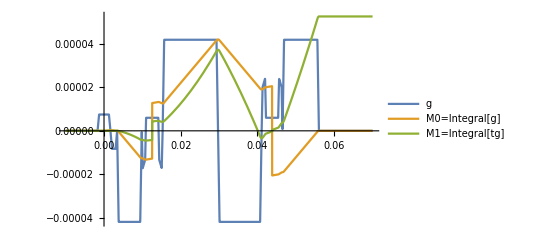
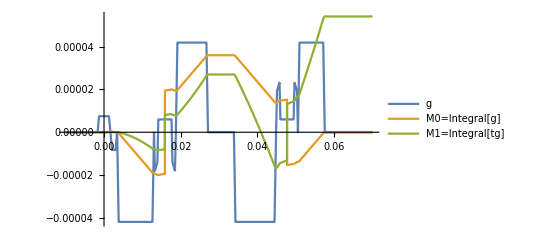
```mathematica
dirPlot=3;
(*Plot[{subs[Gslice[t,dirPlot]]/.time2/.subamp[dirPlot],ScaleDiagram*subs[Fslice[t,dirPlot]]/.time2/.subamp[dirPlot],50ScaleDiagram*subs[M1slice[t,dirPlot]]/.time2/.subamp[dirPlot]},{t,-10000*10^-6,70000*10^-6},PlotRange->Full,PlotLegends->{"g","M0=Integral[g]","M1=Integral[tg]"}]*)
(* TRSE: -Graphics-*)
(* TRSEadj: -Graphics-*)
```

```mathematica
integral M2;
iM2dtrap[DurationGrad_,RampTime_,AmpGrad_,ll_,ul_]=Simplify[Refine[FiInt[t^2*trap[wid,RampTime,amp,t-ll],ll,ul],Assumptions->{wid>0,RampTime>0,ul>0,wid>RampTime}]]/.wid->DurationGrad/.amp->AmpGrad;
```

```mathematica
dir=1;
While[dir<ndir+1,AmpIntM2SliceAtT1[dir]=subs[ iM2dtrap[Gsl90t,ϵ,Gsl90,0,t1]/2.+iM2dtrap[Gsrft,ϵ,Gsrf,t1,t1+Gsrft+ϵ]+iM2dtrap[δ1,ϵ,SignDelta[[1]]*Gds,t2,t3]+iM2dtrap[Crut,RampCrushers,-Gcs,t3,t3+Crut+RampCrushers]+iM2dtrap[Gsl180t,RampGsl180,Gsl180,t3,T1]]/.time2/.subamp[dir];

AmpIntM2SliceAtT2[dir]=subs[AmpIntM2SliceAtT1[dir]+iM2dtrap[Gsl180t,RampGsl180,Gsl180,t3,T1]+iM2dtrap[Crut,RampCrushers,-Gcs,t4-(Crut+RampCrushers),t4]+iM2dtrap[δ2,ϵ,SignDelta[[2]]*Gds,t4,t6]+iM2dtrap[δ11,ϵ,SignDelta[[3]]*Gds,t6,t7]+iM2dtrap[Crut,RampCrushers,Gcs,t7,t7+Crut+RampCrushers]+iM2dtrap[Gsl180t,RampGsl180,Gsl180,t7,T2]]/.time2/.subamp[dir];

M2slice[t_,dir]=(1-UnitStep[t-t1])*iM2dtrap[Gsl90t,ϵ,Gsl90,t1,t+t1]/2.+UnitStep[t-t1]*(iM2dtrap[Gsl90t,ϵ,Gsl90,t1,t+t1]/2.+iM2dtrap[Gsrft,ϵ,Gsrf,t1,t])+
(1-UnitStep[t-T1])*(iM2dtrap[δ1,ϵ,SignDelta[[1]]*Gds,t2,t]+iM2dtrap[Crut,RampCrushers,-Gcs,t3,t]+iM2dtrap[Gsl180t,RampGsl180,Gsl180,t3,t])+
(UnitStep[t-T1]-UnitStep[t-T2])*(-AmpIntM2SliceAtT1[dir]+iM2dtrap[Gsl180t,RampGsl180,Gsl180,t3,t]-iM2dtrap[Gsl180t,RampGsl180,Gsl180,t3,T1]+iM2dtrap[Crut,RampCrushers,-Gcs,t4-(Crut+2RampCrushers),t])+
(1-UnitStep[t-T2])*(iM2dtrap[δ2,ϵ,SignDelta[[2]]*Gds,t4,t]+iM2dtrap[δ11,ϵ,SignDelta[[3]]*Gds,t6,t]+iM2dtrap[Crut,RampCrushers,Gcs,t7,t]+iM2dtrap[Gsl180t,RampGsl180,Gsl180,t7,t])+
UnitStep[t-T2]*(-AmpIntM2SliceAtT2[dir]+
iM2dtrap[Gsl180t,RampGsl180,Gsl180,t7,t]-iM2dtrap[Gsl180t,RampGsl180,Gsl180,t7,T2]+iM2dtrap[Crut,RampCrushers,Gcs,t8-(Crut+RampCrushers),t])+iM2dtrap[δ22,ϵ,SignDelta[[4]]*Gds,t8,t];

dir++];
dir=1;
```

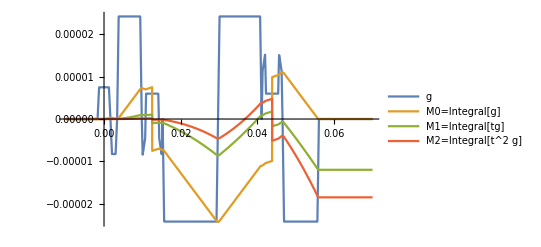
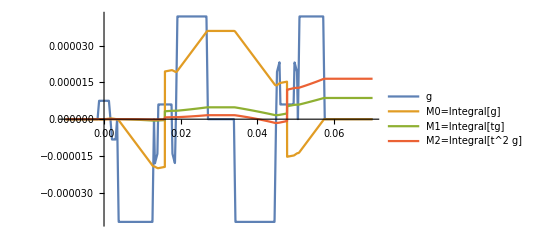
```mathematica
dirPlot=3;
(*Plot[{subs[Gslice[t,dirPlot]]/.time2/.subamp[dirPlot],ScaleDiagram*subs[Fslice[t,dirPlot]]/.time2/.subamp[dir],20ScaleDiagram*subs[M1slice[t,dirPlot]]/.time2/.subamp[dir],10 ScaleDiagram^2*subs[M2slice[t,dirPlot]]/.time2/.subamp[dir]},{t,-10000*10^-6,70000*10^-6},PlotRange->Full,PlotLegends->{"g","M0=Integral[g]","M1=Integral[tg]","M2=Integral[t^2 g]"}]*)
(* TRSE: -Graphics- *)
(* TRSEadj: -Graphics-*)
```